```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v3/phase/phase_boundaryv3

```mathematica
mf=Table[Transpose[Import["./TemB"<>ToString[i]<>"/BUFFER/MF.DAT"]][[1]],{i,1,38}];
intdmfdt=Table[-D[Interpolation[mf[[i]]][x],x],{i,1,38}];
mub=Flatten[{Table[i*15,{i,1,38}]}];
Tpc=Table[FindMaximum[{intdmfdt[[i]],90<x<170},{x,140}][[2]][[1]][[2]],{i,1,38}];
peak=Table[FindMaximum[{intdmfdt[[i]],90<x<170},{x,140}][[1]],{i,1,38}];
Tpcup80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]+2}][[1]][[2]],{i,1,38}];
Tpcdown80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]-5}][[1]][[2]],{i,1,38}];
fitTpc=FindFit[Transpose[{mub,Tpc}],a+b x^2+c x^4(*+d x^6*),{a,b,c},x];
fitTpcup=FindFit[Transpose[{mub,Tpcup80}],a+b x^2+c x^4,{a,b,c},x];
fitTpcdown=FindFit[Transpose[{mub,Tpcdown80}],a+b x^2+c x^4,{a,b,c},x];
```

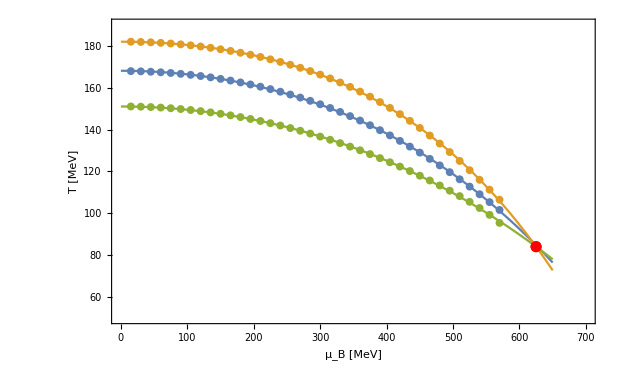

./parav3.pdf

```mathematica
Show[ListPlot[{Transpose[{mub,Tpc}],Transpose[{mub,Tpcup80}],Transpose[{mub,Tpcdown80}]},PlotRange->{{0,700},{50,190}}],Plot[{a+b x^2+c x^4/.fitTpc,a+b x^2+c x^4/.fitTpcup,a+b x^2+c x^4/.fitTpcdown},{x,0,650}],ListPlot[{{625,84}},PlotStyle->Red],Frame->True,FrameLabel->{Style["μ_B [MeV]",15,Black],Style["T [MeV]",15,Black]}]
Export["./parav3.pdf",%]
```

```mathematica
FindRoot[(a+b x^2+c x^4/.fitTpcup)==(a+b x^2+c x^4/.fitTpcdown),{x,600}]
```

{x→625.071}

```mathematica
a+b x^2+c x^4/.fitTpcup/.{x->625.0708654912324}
```

84.004